```mathematica
UnitForm[units_][quantity_]:=UnitConvert[quantity,units]
```

### Constants

```mathematica
filters={"Blue","Yellow","Red","NoFilter"};
colorFilters=filters[[;;3]];
colorWavelengths=Quantity[{4495,5490,6500},"Angstroms"];
color=<|"NoFilter"->(Gray&),"Red"->(Red&),"Blue"->(Blue&),"Yellow"->(Green&)|>;
samples={"White","BK7","SF58"};
sampleThickness=Quantity[{1.036,0.956,1.272},"cm"];
magnetism={5,-90,-166,-259,-5,83,167,243};
```

### Hysteresis

```mathematica
{{0, 0, 0.69}, {5.6, 0.23, 46.33}, {10.1, 0.42, 88.14}, {15.2, 0.64, 127.26}, {20.4, 0.85, 170.02}, {24.9, 1.04, 204.09}, {30.4, 1.27, 250.5}, {24.7, 1.03, 213.04}, {20.3, 0.84, 178.63}, {15.2, 0.63, 132.31}, {10.1, 0.42, 91.1}, {5.6, 0.23, 52.94}, {0, 0, 5.51}, {-5.1, -0.21, -39.8}, {-10.2, -.42, -90.45}, {-15.2, -.63, -124.39}, {-20.4, -.85, -165.92}, {-25, -1.04, -201.95}, {-30, -1.26, -259.3}, {-25, -1.03, -209.86}, {-20.2, -.83, -180.19}, {-15, -.62, -130.42}, {-10.2, -.42, -91.94}, {-5.1, -.21, -48.81}, {0, 0, -5.18}, {5, 0.2, 37.81}, {10.2, 0.42, 83.00}, {14.9, .62, 119.29}, {20.4, .84, 166.92}, {24.9, 1.03, 211.65}, {30.5, 1.26, 243.7}}ᵀ;
{V,A,B}=Quantity@@@({%,{"Volts","Amps","Milliteslas"}}ᵀ)
```

{{0 V,5.6 V,10.1 V,15.2 V,20.4 V,24.9 V,30.4 V,24.7 V,20.3 V,15.2 V,10.1 V,5.6 V,0 V,-5.1 V,-10.2 V,-15.2 V,-20.4 V,-25 V,-30 V,-25 V,-20.2 V,-15 V,-10.2 V,-5.1 V,0 V,5 V,10.2 V,14.9 V,20.4 V,24.9 V,30.5 V},{0 A,0.23 A,0.42 A,0.64 A,0.85 A,1.04 A,1.27 A,1.03 A,0.84 A,0.63 A,0.42 A,0.23 A,0 A,-0.21 A,-0.42 A,-0.63 A,-0.85 A,-1.04 A,-1.26 A,-1.03 A,-0.83 A,-0.62 A,-0.42 A,-0.21 A,0 A,0.2 A,0.42 A,0.62 A,0.84 A,1.03 A,1.26 A},{0.69 mT,46.33 mT,88.14 mT,127.26 mT,170.02 mT,204.09 mT,250.5 mT,213.04 mT,178.63 mT,132.31 mT,91.1 mT,52.94 mT,5.51 mT,-39.8 mT,-90.45 mT,-124.39 mT,-165.92 mT,-201.95 mT,-259.3 mT,-209.86 mT,-180.19 mT,-130.42 mT,-91.94 mT,-48.81 mT,-5.18 mT,37.81 mT,83. mT,119.29 mT,166.92 mT,211.65 mT,243.7 mT}}

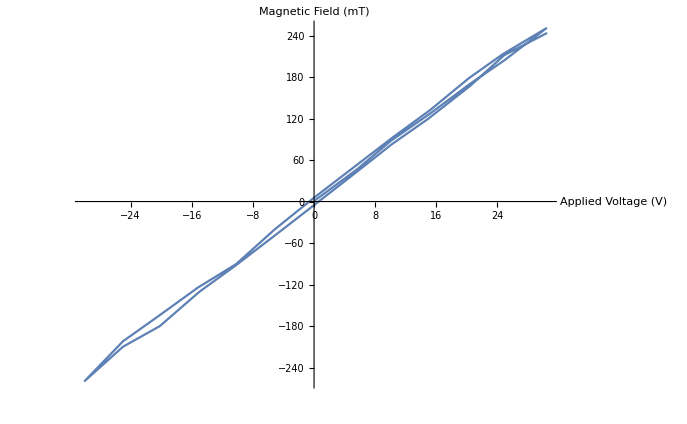

```mathematica
ListPlot[{V,B}ᵀ,Joined->True,AxesLabel->{"Applied Voltage (V)","Magnetic Field (mT)"}]
```

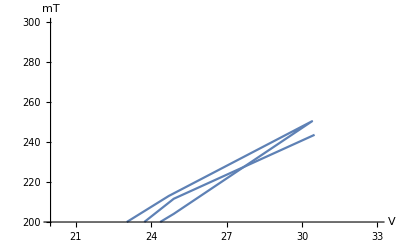

```mathematica
ListPlot[{V,B}ᵀ,Joined->True,PlotRange->{{20,33},{200,300}},AxesLabel->Automatic]
```

### Malus Law

```mathematica
FitMalusFull[filter_]:=
Module[{rawData,n,chunks,μ,σ,around,angles,fit},
rawData=-Rest[Import[NotebookDirectory[]<>"Malus"<>filter<>".xlsx","XLSX"][[1]]]ᵀ[[2]];
n=Length@rawData/10-1;
{μ,σ}=Table[#@rawData[[10i+1;;10i+10]]&/@{Mean,StandardDeviation},{i,0,n}]ᵀ;
around=Around@@@({μ,σ}ᵀ);
angles=Range[0,10n+1,10]°;
fit=NonlinearModelFit[{angles,μ}ᵀ,Subscript[m, 1]-Subscript[m, 2] Cos[θ -Subscript[m, 3]]^2,{Subscript[m, 1],Subscript[m, 2],Subscript[m, 3]},θ,Weights->1/σ^2,VarianceEstimatorFunction->(1&)];
(*Print@Show[
ListPlot[{angles/°,around}ᵀ,ColorFunction->color[filter]],
Plot[fit//Normal,{θ,0,angles[[-1]]},ColorFunction->color[filter]]
];*)
fit
(*Print[fit];
Print[fit["ParameterTable"]];
Print@Show[
ListPlot[{angles,around}ᵀ,ColorFunction->color[filter]],
Plot[fit//Normal,{θ,0,angles[[-1]]},ColorFunction->color[filter]]
]*)
]
```

```mathematica
minMalusAngle=Table[(Subscript[m, 3]/.FitMalusFull[filter]["BestFitParameters"]),{filter,colorFilters}]
%+π/2
minMalusAngleByFilter=<|"Blue"->minMalusAngle[[1]],"Yellow"->minMalusAngle[[2]],"Red"->minMalusAngle[[3]]|>
```

{1.10467,1.10733,1.10712}

{2.67547,2.67813,2.67792}

<|Blue→1.10467,Yellow→1.10733,Red→1.10712|>

```mathematica
Table[FitMalusFull[filter]["RSquared"],{filter,colorFilters}]
```

{0.999836,0.99856,0.999485}

```mathematica
FitMalusFull[filters[[2]]]
```

FittedModel[0.00061743+0.0390204 Cos[1.10733-θ]^2]

```mathematica
field[i_]:=magnetism[[Floor[i/9]+1]];
sample[i_]:=samples[[Mod[Floor[i/3],3]+1]];
filter[i_]:=colorFilters[[Mod[i,3]+1]];
startAngles=Table@@@{{195, 9}, {190, 2}, {195, 4}, {200, 3}, {180, 1}, {190, 2}, {200, 1}, {195, 2}, {200, 3}, {175, 1}, {185, 1}, {190, 1}, {200, 1}, {195, 1}, {200, 4}, {195, 1}, {200, 5}, {195, 3}, {200, 9}, {210, 3}, {200, 3}, {195, 2}, {200, 1}, {220, 1}, {215, 2}, {195, 1}, {205, 1}, {190, 2}, {195, 2}}//Flatten;
minAngles=Import[NotebookDirectory[]<>"MinAngleEye.xlsx","XLSX"][[1]]ᵀ[[1]]
```

{153.,153.,154.,151.,151.,155.,154.,154.,152.,146.,148.,150.,152.,153.,149.,156.,156.,154.,135.,143.,144.,155.,150.,150.,155.,155.,154.,130.,139.,144.,156.,151.,154.,157.,157.,158.,151.,158.,153.,155.,151.,151.,149.,150.,152.,160.,159.,157.,156.,155.,154.,155.,152.,151.,165.,163.,161.,154.,154.,155.,149.,149.,152.,175.,167.,163.,148.,159.,146.,143.,147.,148.}

```mathematica
Table[{i,field@i,sample@i,filter@i,startAngles[[i+1]]},{i,0,8*9-1}]//TableForm;
```

```mathematica
startAngle
```

startAngle

```mathematica
ClearAll@FitFaradata
geti[field_,sample_,filter_]:=3^2(Position[magnetism,field][[1,1]]-1)+3(Position[samples,sample][[1,1]]-1)+Position[colorFilters,filter][[1,1]]-1;
(*FitFaradata[field_,sample_,filter_,opts:OptionsPattern[{plot->False,params->False}]]:=FitFaradata[
3^2(Position[magnetism,field][[1,1]]-1)+3(Position[samples,sample][[1,1]]-1)+Position[colorFilters,filter][[1,1]]-1,
opts
];*)
(*FitFaradata[i_,opts:OptionsPattern[{plot->False,params->False}]]:=*)
FitFaradata[field_,sample_,filter_,opts:OptionsPattern[{plot->False,params->False}]]:=Module[
{
angleStart=startAngles[[geti[field,sample,filter]+1]],
rawData,n,chunks,μ,σ,around,angles,fit,degreeFn
},
(*Print[NotebookDirectory[]<>ToString@field<>sample<>filter<>"Min.xlsx"];*)
rawData=-Rest[Import[NotebookDirectory[]<>ToString@field<>sample<>filter<>"Min.xlsx","XLSX"][[1]]]ᵀ[[2]];
(*startAngle=startAngles[[0+1]];*)
(*Print[geti[field,sample,filter]];
Print[angleStart];*)
n=Length@rawData/10-1;
{angles,μ,σ}=Table[Join[{angleStart-10j}°,#@rawData[[10j+1;;10j+10]]&/@{Mean,StandardDeviation}],{j,0,n}]ᵀ;
around=Around@@@({μ,σ}ᵀ);
fit=NonlinearModelFit[{angles,μ}ᵀ,Subscript[m, 1]-Subscript[m, 2] Cos[θ-Subscript[m, 3]]^2,{Subscript[m, 1],Subscript[m, 2],Subscript[m, 3]},θ,Weights->1/σ^2,VarianceEstimatorFunction->(1&)];
degreeFn=Normal@fit/.θ->(θ °);
If[OptionValue[params],
Print[fit["ParameterTable"]]
];
If[OptionValue[plot],
Print@Show[
ListPlot[{angles /°,around}ᵀ,ColorFunction->color[filter],PlotRange->{{110,230},Automatic},AxesLabel->{"Angle (Degrees)","Intensity (V)"},PlotMarkers->None],
Plot[degreeFn,{θ,angles[[1]]/°,angles[[-1]]/°},ColorFunction->color[filter]]
]
];
fit
]
```

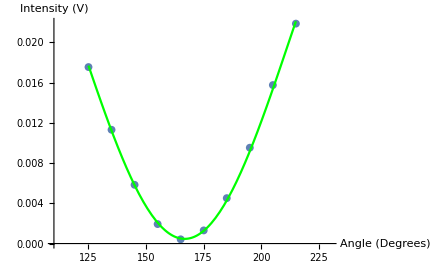

FittedModel[0.000467413+0.0388615 Cos[1.33939-θ]^2]

0.999772

```mathematica
FitFaradata[magnetism[[-1]],"White","Yellow",plot->True]
%["RSquared"]
```

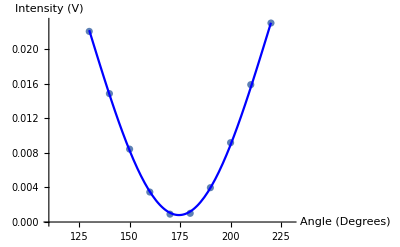
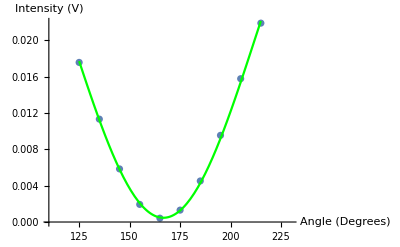
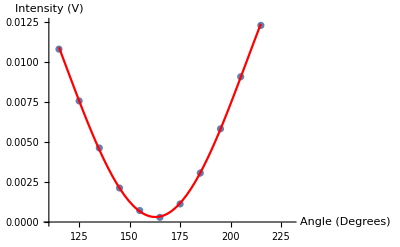
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-]
```

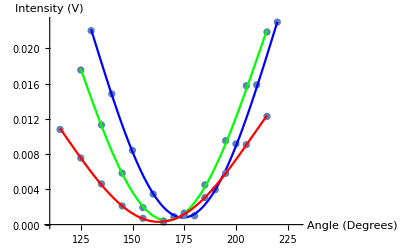

```mathematica
Table[minAngles[[geti[field,"White","Blue"]+1]]°-π/2//N,{field,magnetism}]
```

{1.09956,0.977384,0.785398,0.698132,1.06465,1.22173,1.309,1.48353}

```mathematica
Table[Subscript[m, 3]/.FitFaradata[field,"White","Blue"]["BestFitParameters"],{field,magnetism}]
```

{1.10421,0.973662,0.832906,0.744735,1.10421,1.22895,1.35585,1.47367}

```mathematica
ClearAll@B;
CalculateVerdet1[sample_,filter_]:=Module[
{radsVsB,fit,Vd,σVd,yint,σyint},
radsVsB=Table[{field,minAngles[[geti[field,sample,filter]+1]]°-π/2-minMalusAngleByFilter[[filter]]},{field,magnetism}];
(*Print@radsVsB;*)
(*ListPlot[radsVsB,ColorFunction->color[filter]];*)
fit=LinearModelFit[radsVsB,B,B];
{yint,Vd}=fit["BestFitParameters"];
{σyint,σVd}=fit["ParameterErrors"];
Vd=Around[Vd,σVd];
yint=Around[yint,σyint];
{radsVsB,Quantity[Vd,"Radians/Teslas"]/sampleThickness[[Position[samples,sample][[1,1]]]]//UnitForm@"Radians/Tesla/Meter",Normal@fit,yint,Vd,fit}
]
```

```mathematica
Table[Flatten@{{sample},{filter},CalculateVerdet1[sample,filter][[2;;]]},{sample,samples},{filter,colorFilters}]//TableForm
```

White
Blue
(0.1500.006) rad/(m T)
-0.0204804+0.00155316 B
-0.0200.010
0.001550.00006 | White
Yellow
(0.0970.008) rad/(m T)
0.00807306+0.00100318 B
0.0080.012
0.001000.00008 | White
Red
(0.0700.005) rad/(m T)
-0.00119791+0.000728443 B
-0.0010.008
0.000730.00005
BK7
Blue
(-0.0170.010) rad/(m T)
0.000981571-0.000162476 B
0.0000.016
-0.000160.00010 | BK7
Yellow
(0.0260.008) rad/(m T)
-0.00709021+0.000249252 B
-0.0070.012
0.000250.00008 | BK7
Red
(-0.0060.014) rad/(m T)
-0.0295502-0.0000614917 B
-0.0300.022
-0.000060.00014
SF58
Blue
(-0.0320.009) rad/(m T)
-0.0193205-0.000405046 B
-0.0190.019
-0.000410.00012 | SF58
Yellow
(-0.0270.005) rad/(m T)
-0.0174395-0.000340802 B
-0.0170.010
-0.000340.00006 | SF58
Red
(-0.0220.004) rad/(m T)
-0.0148682-0.000275913 B
-0.0150.007
-0.000280.00005

```mathematica
ClearAll@B;
CalculateVerdet2[sample_,filter_]:=Module[
{radsVsB,fit,Vd,σVd,yint,σyint},
radsVsB=Table[{field,(Subscript[m, 3]/.FitFaradata[field,sample,filter,plot->False]["BestFitParameters"])-minMalusAngleByFilter[[filter]]},{field,magnetism}];
(*Print@radsVsB;*)
(*ListPlot[radsVsB,ColorFunction->color[filter]];*)
fit=LinearModelFit[radsVsB,B,B];
{yint,Vd}=fit["BestFitParameters"];
{σyint,σVd}=fit["ParameterErrors"];
Vd=Around[Vd,σVd];
yint=Around[yint,σyint];
{radsVsB,Quantity[Vd,"Radians/Teslas"]/sampleThickness[[Position[samples,sample][[1,1]]]]//UnitForm@"Radians/Tesla/Meter",Normal@fit}
]
```

```mathematica
Table[
{sample,samples},{filter,colorFilters}
]
```

```mathematica
Flatten[Table[{sample,filter,CalculateVerdet2[sample,filter][[2]],CalculateVerdet2[sample,filter][[3]]},{sample,samples},{filter,colorFilters}],1]//TeXForm
```

\left(
\begin{array}{cccc}
 \text{White} & \text{Blue} & (0.1434\pm 0.0033)\text{rad}\text{/(}\text{m}\, \text{T}) & 0.00148562 B+0.00168611 \\
 \text{White} & \text{Yellow} & (0.091\pm 0.008)\text{rad}\text{/(}\text{m}\, \text{T}) & 0.000944911 B+0.0084611 \\
 \text{White} & \text{Red} & (0.066\pm 0.008)\text{rad}\text{/(}\text{m}\, \text{T}) & 0.000681233 B+0.00921698 \\
 \text{BK7} & \text{Blue} & (-0.008\pm 0.008)\text{rad}\text{/(}\text{m}\, \text{T}) & -0.0000780567 B-0.0155448 \\
 \text{BK7} & \text{Yellow} & (-0.003\pm 0.007)\text{rad}\text{/(}\text{m}\, \text{T}) & -0.0000330493 B-0.0092144 \\
 \text{BK7} & \text{Red} & (-0.004\pm 0.008)\text{rad}\text{/(}\text{m}\, \text{T}) & -0.0000368284 B-0.00148362 \\
 \text{SF58} & \text{Blue} & (-0.0526\pm 0.0008)\text{rad}\text{/(}\text{m}\, \text{T}) & -0.000669452 B-0.0220403 \\
 \text{SF58} & \text{Yellow} & (-0.0304\pm 0.0011)\text{rad}\text{/(}\text{m}\, \text{T}) & -0.000386321 B-0.0103541 \\
 \text{SF58} & \text{Red} & (-0.0215\pm 0.0005)\text{rad}\text{/(}\text{m}\, \text{T}) & -0.000273009 B-0.0112041 \\
\end{array}
\right)

```mathematica
Flatten[Table[{sample,filter,CalculateVerdet2[sample,filter][[3]]},{sample,samples},{filter,colorFilters}],1]//TableForm
```

White | Blue | 0.00168611+0.00148562 B
White | Yellow | 0.0084611+0.000944911 B
White | Red | 0.00921698+0.000681233 B
BK7 | Blue | -0.0155448-0.0000780567 B
BK7 | Yellow | -0.0092144-0.0000330493 B
BK7 | Red | -0.00148362-0.0000368284 B
SF58 | Blue | -0.0220403-0.000669452 B
SF58 | Yellow | -0.0103541-0.000386321 B
SF58 | Red | -0.0112041-0.000273009 B

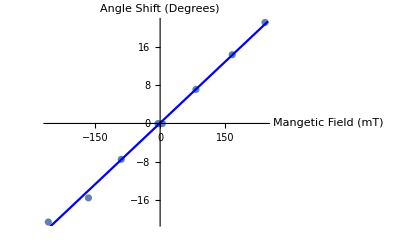
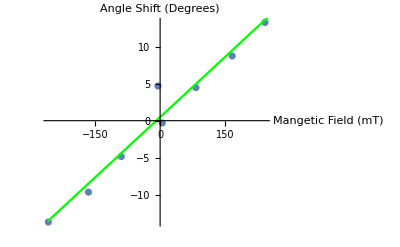
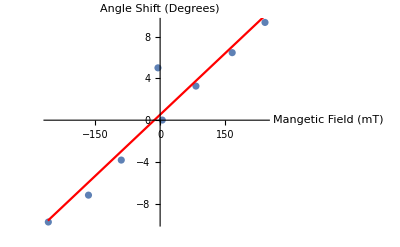
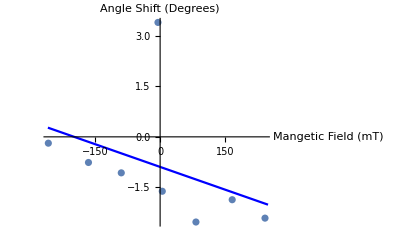
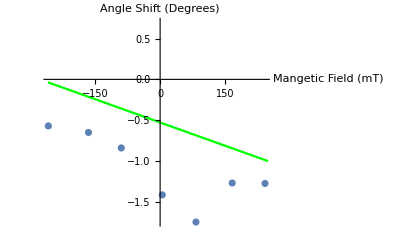
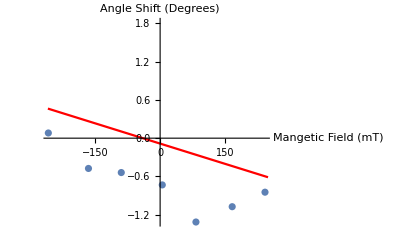
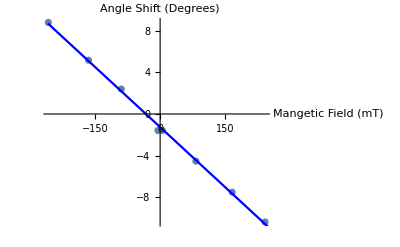
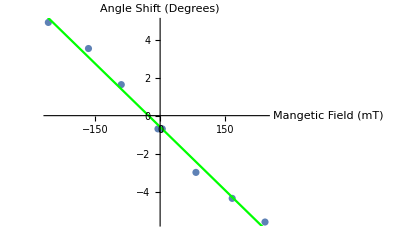

```mathematica
Table[
(
verdetStuff=CalculateVerdet2[sample,filter];
{mT,rads}=verdetStuff[[1]]ᵀ;
degs=rads/°;
Show[
ListPlot[{mT,degs}ᵀ,ColorFunction->color[filter],AxesLabel->{"Mangetic Field (mT)","Angle Shift (Degrees)"}],
Plot[verdetStuff[[3]]/°,{B,-260,250},ColorFunction->color[filter]]
]
),
{sample,samples},
{filter,colorFilters}
]
```

```mathematica
(*Verdet2=Association[Table[{sample,filter}->CalculateVerdet2[sample,filter],{sample,samples},{filter,colorFilters}]];*)
Table[(
Verdet=Table[CalculateVerdet2[sample,filter],{filter,colorFilters}];
points=Table[{#[[1]],#[[2]]/°}&/@Verdet[[filter,1]],{filter,3}];
fits=Table[Verdet[[filter,3]]/°,{filter,3}];
Show[
ListPlot[points,PlotStyle->{Blue,Green,Red},PlotMarkers->Automatic,PlotLegends->Placed[Table[Verdet[[filter,3]],{filter,3}],Center],AxesLabel->{"Mangetic Field (mT)","Angle Shift (Degrees)"}],
Plot[fits,{B,-260,250},PlotStyle->{Blue,Green,Red}]
]
),{sample,samples}
]
```

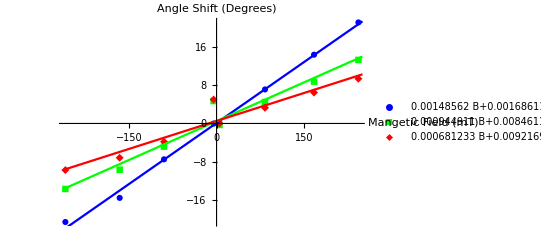
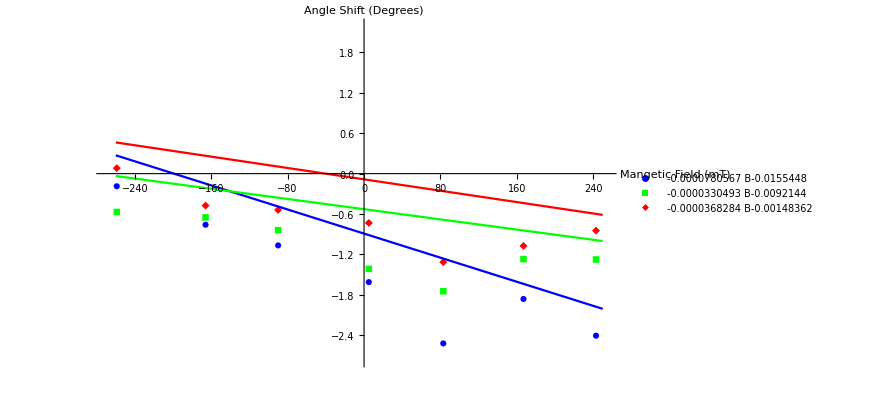
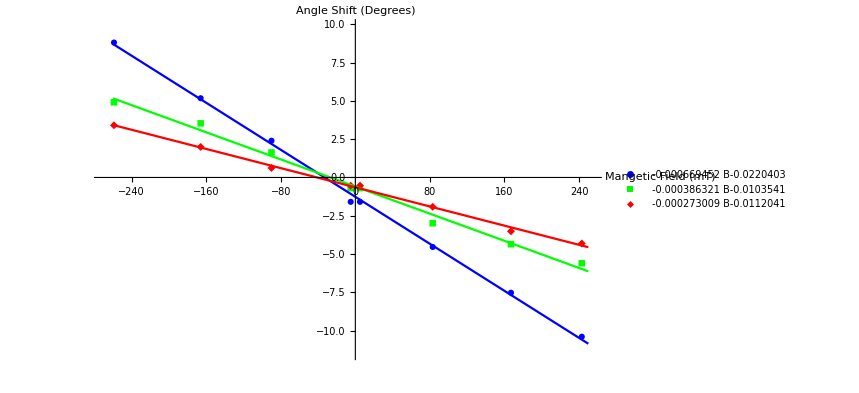

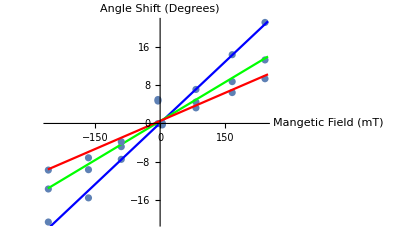
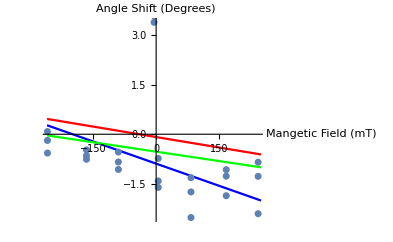
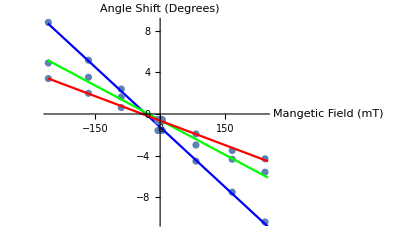

```mathematica
Show[#,PlotLegends->colorFilters]&/@
Apply[
Show,
Table[
(
verdetStuff=CalculateVerdet2[sample,filter];
{mT,rads}=verdetStuff[[1]]ᵀ;
degs=rads/°;
Show[
ListPlot[{mT,degs}ᵀ,ColorFunction->color[filter],AxesLabel->{"Mangetic Field (mT)","Angle Shift (Degrees)"}],
Plot[verdetStuff[[3]]/°,{B,-260,250},ColorFunction->color[filter]]
]
),
{sample,samples},
{filter,colorFilters}
],
1
]
```

```mathematica
magnetism[[-1]]
```

243

```mathematica
whiteSampleBlueFilterRadians=Table[{field,(Subscript[m, 3]/.FitFaradata[field,"White","Blue"]["BestFitParameters"])-minMalusAngleByFilter[["Blue"]]},{field,magnetism}]
```

{{5,-0.000461311},{-90,-0.131012},{-166,-0.271768},{-259,-0.359939},{-5,-0.000461311},{83,0.124275},{167,0.251173},{243,0.368999}}

FittedModel[0.00168611+0.00148562 b]

1.4340.03310^-7 rad/(cm G)

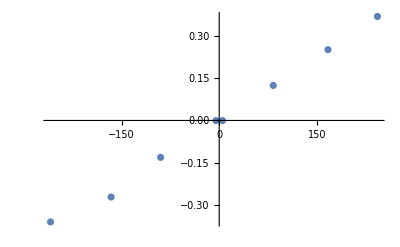

```mathematica
fit=LinearModelFit[whiteSampleBlueFilterRadians,b,b]
Vd=fit["BestFitParameters"][[2]];
σVd=fit["ParameterErrors"][[2]];
Vd=Around[Vd,σVd];
Quantity[Vd,"Radians/Teslas"]/sampleThickness[[1]]//UnitForm@"Radians/Gauss/Centimeter"
ListPlot[whiteSampleBlueFilterRadians]
```

```mathematica
fit["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

```mathematica
fit["ParameterTable"]
fit["ParameterErrors"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.00168611 | 0.00543838 | 0.310039 | 0.767017
b | 0.00148562 | 0.0000346902 | 42.8253 | 1.08487×10^-8

{0.00543838,0.0000346902}

```mathematica
Table[{field,θ/.FindMaximum[FitFaradata[field,"White","Blue"]//Normal,{θ,2.7}][[2]]},{field,magnetism}]
(*Flatten[□,1]*)
```

{{5,2.67501},{-90,2.63173},{-166,2.6655},{-259,2.6646},{-5,2.67501},{83,2.71248},{167,2.66484},{243,2.60814}}

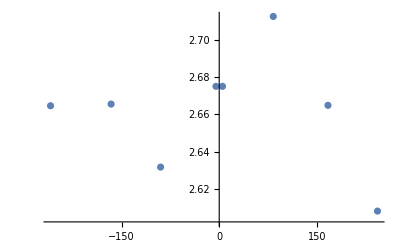

```mathematica
ListPlot[%]
```